```mathematica
s=19;
k=RandomReal[10];
```

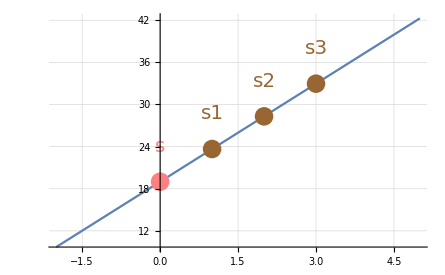

```mathematica
Show[
Plot[k*x+s, {x,-2, 5}, GridLines->Automatic],
Graphics[{PointSize[0.03],Pink,Point[{0,s}], Text[Style["s", 20], {0, 24}]}],
Graphics[{PointSize[0.03], Brown, Point[{{1,k*1+s},{2, k*2+s}, {3, k*3+s}}], Text[Style["s1", 20], {1, k*1+s+5}], 
Text[Style["s2", 20], {2, k*2+s+5}],
Text[Style["s3", 20], {3, k*3+s+5}]}]
]
```

```mathematica
SetDirectory@NotebookDirectory[];
map = Import["treasure_map_small.jpg"]
```

-Graphics-

```mathematica
map=ColorConvert[map,"Grayscale"]
```

-Graphics-

```mathematica
Dimensions[ImageData[map]]
```

{300,400}

```mathematica
ShamirShare[s_]:=
Module[{k=RandomReal[1000]},
s1=1*k+s;
s2=2*k+s;
s3=3*k+s;
Return[{s1,s2,s3}]
]
ShamirDec[s1_, s2_]:=
Module[{},
ClearAll[k,s];
r=Solve[{1*k+s==s1, 2*k+s==s2}, {k, s}];
s=r[[All,2, 2]];
Return[s[[1]]]
]
```

```mathematica
ShamirShare[189]
```

{448.007,707.014,966.02}

```mathematica
ShamirDec[448.00677911634216,707.0135582326843]
```

189.

```mathematica
shares = ShamirShare/@Flatten[ImageData[map]];
share1=shares[[All, 1]];
share2=shares[[All,2]];
share3=shares[[All,3]];
normshare1=Standardize[share1];
normshare2=Standardize[share2];
normshare3=Standardize[share3];

map1=ArrayReshape[normshare1,{300,400}];
map2=ArrayReshape[normshare2,{300,400}];
map3=ArrayReshape[normshare3,{300,400}];
```

```mathematica
Image[map1, ColorSpace->"Grayscale"]
Image[map2, ColorSpace->"Grayscale"]
Image[map3, ColorSpace->"Grayscale"]
```

-Graphics-

-Graphics-

-Graphics-

```mathematica
ShamirDec[share1[[1]],share2[[1]]]
```

1.

```mathematica
recoverMap = MapThread[ShamirDec,{share1, share2}];
```

```mathematica
recoverMapMap=ArrayReshape[recoverMap,{300,400}];
```

```mathematica
Image[recoverMapMap]
```

-Graphics-

```mathematica
recoverMap = MapThread[ShamirDec,{share1, share3}];
recoverMapMap=ArrayReshape[recoverMap,{300,400}];
Image[recoverMapMap]
```

-Graphics-